#### Matrices

```mathematica
ClearAll["Global`*"];

eqs={F[1]==Ct[1]/(1+Sum[KK[1,j]F[j],{j,1,2}]),
F[2]==Ct[2]/(1+Sum[KK[2,j]F[j],{j,1,2}])
};
KK[1,2]=KK[2,1]
eqs
```

KK[2,1]

{F[1]==Ct[1]/(1+F[1] KK[1,1]+F[2] KK[2,1]),F[2]==Ct[2]/(1+F[1] KK[2,1]+F[2] KK[2,2])}

```mathematica
Solve[eqs,{F[1],F[2]}][[1]]
```

```mathematica
Qmat ={{F[1]KK[1,1]+1+Sum[KK[1,j]F[j],{j,1,2}], F[1]KK[1,2]},{ F[2]KK[2,1], F[2]KK[2,2]+1+Sum[KK[2,j]F[j],{j,1,2}]}}
Qmat//MatrixForm
```

{{1+2 F[1] KK[1,1]+F[2] KK[2,1],F[1] KK[2,1]},{F[2] KK[2,1],1+F[1] KK[2,1]+2 F[2] KK[2,2]}}

(1+2 F[1] KK[1,1]+F[2] KK[2,1] | F[1] KK[2,1]
F[2] KK[2,1] | 1+F[1] KK[2,1]+2 F[2] KK[2,2])

```mathematica
nd = 4;
Qf = Table[F[i]*KK[i,j],{i,1,nd},{j,1,nd}];
Qd = DiagonalMatrix[Table[1+Sum[KK[i,j]F[j],{j,1,nd}],{i,1,nd}]];
Qmat = Qf+Qd;
```

```mathematica
expr=Adjugate[Qmat][[1,2]]//Factor;
```

```mathematica
expr=Det[Qmat];
```

```mathematica
expr/. KK[_,_]->1
```

F[1] (-1-2 F[1]-F[1]^2-2 F[2]-2 F[1] F[2]-F[2]^2-2 F[3]-2 F[1] F[3]-2 F[2] F[3]-F[3]^2-2 F[4]-2 F[1] F[4]-2 F[2] F[4]-2 F[3] F[4]-F[4]^2)

```mathematica
(*1. Extract F[i] and KK[i,j] variables*)vars=DeleteDuplicates@Cases[expr,F[i_]|KK[i_,j_]:>F[i],{0,Infinity}];
kkVars=DeleteDuplicates@Cases[expr,KK[i_,j_]:>KK[i,j],{0,Infinity}];

(*2. Combine all variables*)
allVars=Union[vars,kkVars];

(*3. Build positivity assumptions*)
assumptions=Thread[allVars>0];

(*4. Apply Assuming block to extract signs of each term*)terms=List@@Expand[expr];
signs=Assuming[assumptions,Simplify[Sign/@terms]]
```

{-1,-1,1,-1,-1}

```mathematica
expr
```

-F[1] (KK[2,1]+F[1] KK[2,1] KK[3,1]-F[3] KK[1,3] KK[3,2]+F[2] KK[2,1] KK[3,2]+2 F[3] KK[2,1] KK[3,3])

```mathematica
kkTerms=DeleteDuplicates@Cases[expr,KK[i_,j_]:>{i,j},All];
unorderedPairs=DeleteDuplicates[Sort/@kkTerms];
pairRules=Association[Table[Sort[pair]->RandomReal[{0.1,10}],{pair,unorderedPairs}]];
kkRules=Map[Function[{ij},KK[Sequence@@ij]->pairRules[Sort[ij]]],kkTerms];
fList=DeleteDuplicates@Cases[expr,F[i_]:>F[i],All];
fRules=Thread[fList->RandomReal[{0.1,10},Length[fList]]];
expr/. kkRules//Factor
```

-448.804 F[1] (0.0122792+0.221634 F[1]+1. F[1]^2+0.134323 F[2]+1.20536 F[1] F[2]+0.248993 F[2]^2-0.104187 F[3]-0.920489 F[1] F[3]+0.111215 F[2] F[3]-0.758863 F[3]^2+0.121591 F[4]+1.09791 F[1] F[4]+0.684907 F[2] F[4]-0.4849 F[3] F[4]+0.300172 F[4]^2)

```mathematica
expr//Factor
```

-F[1] (KK[2,1]+F[1] KK[2,1] KK[3,1]-F[3] KK[1,3] KK[3,2]+F[2] KK[2,1] KK[3,2]+2 F[3] KK[2,1] KK[3,3]+F[4] KK[2,1] KK[3,4]+F[1] KK[2,1] KK[4,1]+F[1]^2 KK[2,1] KK[3,1] KK[4,1]-F[1] F[3] KK[1,3] KK[3,2] KK[4,1]+F[1] F[2] KK[2,1] KK[3,2] KK[4,1]+2 F[1] F[3] KK[2,1] KK[3,3] KK[4,1]+F[1] F[4] KK[2,1] KK[3,4] KK[4,1]-F[4] KK[1,4] KK[4,2]+F[2] KK[2,1] KK[4,2]-F[1] F[4] KK[1,4] KK[3,1] KK[4,2]+F[1] F[2] KK[2,1] KK[3,1] KK[4,2]-F[2] F[3] KK[1,3] KK[3,2] KK[4,2]-F[2] F[4] KK[1,4] KK[3,2] KK[4,2]+F[2]^2 KK[2,1] KK[3,2] KK[4,2]-2 F[3] F[4] KK[1,4] KK[3,3] KK[4,2]+2 F[2] F[3] KK[2,1] KK[3,3] KK[4,2]+F[3] F[4] KK[1,3] KK[3,4] KK[4,2]-F[4]^2 KK[1,4] KK[3,4] KK[4,2]+F[2] F[4] KK[2,1] KK[3,4] KK[4,2]+F[3] KK[2,1] KK[4,3]+F[1] F[3] KK[2,1] KK[3,1] KK[4,3]-F[3]^2 KK[1,3] KK[3,2] KK[4,3]+F[3] F[4] KK[1,4] KK[3,2] KK[4,3]+F[2] F[3] KK[2,1] KK[3,2] KK[4,3]+2 F[3]^2 KK[2,1] KK[3,3] KK[4,3]+2 F[4] KK[2,1] KK[4,4]+2 F[1] F[4] KK[2,1] KK[3,1] KK[4,4]-2 F[3] F[4] KK[1,3] KK[3,2] KK[4,4]+2 F[2] F[4] KK[2,1] KK[3,2] KK[4,4]+4 F[3] F[4] KK[2,1] KK[3,3] KK[4,4]+2 F[4]^2 KK[2,1] KK[3,4] KK[4,4])

```mathematica
Expand[Adjugate[Qmat][[1,1]],{F[1],F[2],F[3]}]
```

-F[2] F[3] KK[2,3] KK[3,2]+(1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3]) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3])

```mathematica
Inverse[Qmat]-Minors[Qmat]/Det[Qmat]//PossibleZeroQ//MatrixForm
```

(False | False | True
False | True | False
True | False | False)

```mathematica
MatrixForm[PossibleZeroQ/@(Inverse[Qmat]-Transpose[Minors[Qmat]]/Det[Qmat])]
```

(False | False | False
False | True | False
False | False | False)

```mathematica
MatrixForm[PossibleZeroQ/@(Inverse[Qmat]-Transpose[Minors[Qmat]]/Det[Qmat])]
```

(False | False | False
False | True | False
False | False | False)

```mathematica
Qmat={{a,b},{c,d}};
Inverse[Qmat]-Adjugate[Qmat]/Det[Qmat]//Simplify
```

{{0,0},{0,0}}

```mathematica
Minors[Qmat]/Det[Qmat]//MatrixForm
```

((-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3]))/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3])) | (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3])/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3])) | (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3])/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3]))
(-F[1] F[3] KK[2,1] KK[3,1]+F[3] KK[3,2]+2 F[1] F[3] KK[1,1] KK[3,2]+F[3]^2 KK[1,3] KK[3,2]+F[2] F[3] KK[2,1] KK[3,2])/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3])) | (-F[1] F[3] KK[1,3] KK[3,1]+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3]))/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3])) | (F[1] KK[2,1]+F[1]^2 KK[2,1] KK[3,1]-F[1] F[3] KK[1,3] KK[3,2]+F[1] F[2] KK[2,1] KK[3,2]+2 F[1] F[3] KK[2,1] KK[3,3])/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3]))
(-F[3] KK[3,1]-F[1] F[3] KK[2,1] KK[3,1]-2 F[2] F[3] KK[2,2] KK[3,1]-F[3]^2 KK[2,3] KK[3,1]+F[2] F[3] KK[2,1] KK[3,2])/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3])) | (F[2] KK[2,1]+F[1] F[2] KK[2,1] KK[3,1]-F[2] F[3] KK[2,3] KK[3,1]+F[2]^2 KK[2,1] KK[3,2]+2 F[2] F[3] KK[2,1] KK[3,3])/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3])) | (-F[2] F[3] KK[2,3] KK[3,2]+(1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3]) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3]))/(F[3] (-F[1] KK[1,3]-F[1]^2 KK[1,3] KK[2,1]-2 F[1] F[2] KK[1,3] KK[2,2]-F[1] F[3] KK[1,3] KK[2,3]+F[1] F[2] KK[2,1] KK[2,3]) KK[3,1]-F[3] (-F[1] F[2] KK[1,3] KK[2,1]+F[2] KK[2,3]+2 F[1] F[2] KK[1,1] KK[2,3]+F[2] F[3] KK[1,3] KK[2,3]+F[2]^2 KK[2,1] KK[2,3]) KK[3,2]+(-F[1] F[2] KK[2,1]^2+(1+2 F[1] KK[1,1]+F[3] KK[1,3]+F[2] KK[2,1]) (1+F[1] KK[2,1]+2 F[2] KK[2,2]+F[3] KK[2,3])) (1+F[1] KK[3,1]+F[2] KK[3,2]+2 F[3] KK[3,3])))

```mathematica
Inverse[Qmat]//Simplify//MatrixForm
```

((1+F[1] KK[2,1]+2 F[2] KK[2,2])/(2 F[1]^2 KK[1,1] KK[2,1]+(1+F[2] KK[2,1]) (1+2 F[2] KK[2,2])+F[1] (KK[2,1]+KK[1,1] (2+4 F[2] KK[2,2]))) | -(F[1] KK[2,1])/(2 F[1]^2 KK[1,1] KK[2,1]+(1+F[2] KK[2,1]) (1+2 F[2] KK[2,2])+F[1] (KK[2,1]+KK[1,1] (2+4 F[2] KK[2,2])))
-(F[2] KK[2,1])/(2 F[1]^2 KK[1,1] KK[2,1]+(1+F[2] KK[2,1]) (1+2 F[2] KK[2,2])+F[1] (KK[2,1]+KK[1,1] (2+4 F[2] KK[2,2]))) | (1+2 F[1] KK[1,1]+F[2] KK[2,1])/(2 F[1]^2 KK[1,1] KK[2,1]+(1+F[2] KK[2,1]) (1+2 F[2] KK[2,2])+F[1] (KK[2,1]+KK[1,1] (2+4 F[2] KK[2,2]))))

```mathematica
(1+F[1] KK[2,1]+2 F[2] KK[2,2])/(2 F[1]^2 KK[1,1] KK[2,1]+(1+F[2] KK[2,1]) (1+2 F[2] KK[2,2])+F[1] (KK[2,1]+KK[1,1] (2+4 F[2] KK[2,2])))
```

```mathematica
ClearAll["Global`*"];
(*Parameters*)
(*Parameters*)n=2;  (*Number of species*)

(*Use unprotected variable names*)
cVars=Array[c,n];      (*Variables:c[1],c[2],...,c[n]*)
mParams=Array[m,n];    (*Constants:m[1],m[2],...,m[n]*)
kParams=Array[k,{n,n}];  (*Parameters:k[1,1],...,k[n,n]*)

(*Define the equations*)
eqns=Table[Sum[cVars[[i]] cVars[[j]] kParams[[i,j]],{j,1,n}]+cVars[[i]]-mParams[[i]]==0,{i,1,n}];

(*Compute the Gröbner basis in lex order,eliminate intermediate expressions*)
GroebnerBasis[eqns,cVars,MonomialOrder->Lexicographic]
```

{c[2]^2 k[1,1]-c[2]^2 k[2,1]-c[2]^3 k[1,2] k[2,1]+2 c[2]^3 k[1,1] k[2,2]-c[2]^3 k[2,1] k[2,2]-c[2]^4 k[1,2] k[2,1] k[2,2]+c[2]^4 k[1,1] k[2,2]^2-c[2]^2 k[2,1]^2 m[1]-2 c[2] k[1,1] m[2]+c[2] k[2,1] m[2]+c[2]^2 k[1,2] k[2,1] m[2]-2 c[2]^2 k[1,1] k[2,2] m[2]+k[1,1] m[2]^2,c[2] k[1,1]-c[2] k[2,1]-c[2]^2 k[1,2] k[2,1]+2 c[2]^2 k[1,1] k[2,2]-c[2]^2 k[2,1] k[2,2]-c[2]^3 k[1,2] k[2,1] k[2,2]+c[2]^3 k[1,1] k[2,2]^2-c[2] k[2,1]^2 m[1]-k[1,1] m[2]+k[2,1] m[2]+c[1] k[1,1] k[2,1] m[2]+c[2] k[1,2] k[2,1] m[2]-c[2] k[1,1] k[2,2] m[2],c[2]+c[1] c[2] k[2,1]+c[2]^2 k[2,2]-m[2],c[2]+c[1] c[2] k[1,1]+c[2]^2 k[1,2]+c[2]^2 k[2,2]+c[1] c[2]^2 k[1,1] k[2,2]+c[2]^3 k[1,2] k[2,2]+c[2] k[2,1] m[1]-m[2]-c[1] k[1,1] m[2]-c[2] k[1,2] m[2],c[1]+c[1]^2 k[1,1]+c[1] c[2] k[1,2]-m[1]}

#### Turning points loop

```mathematica
ClearAll["Global`*"];

n=4;

(*Variables*)
cVars=Array[c,n];

SeedRandom[29];  


(*reproducibility*)
mVals=RandomReal[{0.1,100.0},n];

kVals=RandomReal[{0.01,10.0},{n,n}];

(*Parameters for the log-normal distribution*)
μ=1;       (*Mean of the underlying normal distribution*)
σ=5;       (*Standard deviation*)

(*Sample kVals as log-normally distributed*)
kVals=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];
kVals = 0.5(kVals + Transpose[kVals])
kVals//MatrixForm

(*Assign random positive starting point for each variable*)
initialGuess=Table[cVars[[i]]->RandomReal[{0.1,2.0}],{i,1,n}];

mInd = 1;
mRange = Range[0,1000,1];
solArray = {};
soldijArray = {};
Do[
mVals[[mInd]]=mv;
eqnsSym=Table[Sum[cVars[[i]] *cVars[[j]] *kVals[[i,j]]^-1,{j,1,n}]+cVars[[i]]-mVals[[i]],{i,1,n}];
sol=FindRoot[eqnsSym, Table[{cVars[[i]],cVars[[i]]/.initialGuess},{i,1,n}]];
cSol =  cVars/.sol;
AppendTo[solArray,cSol];

dij=kVals^-1*KroneckerProduct[cSol, cSol];

upperTriangleList=Flatten[Table[dij[[i,j]],{i,1,n},{j,i,n}]];
AppendTo[soldijArray,upperTriangleList];

initialGuess=sol;
,{mv,mRange}];
```

{{623.151,105.132,3.45644,3509.32,0.994931,0.323485,414.779,2.35952},{105.132,0.000631874,28.2167,358.898,0.0535047,1482.94,646082.,13790.2},{3.45644,28.2167,14.0469,24717.2,237.606,21.1065,0.00306561,7.85608},{3509.32,358.898,24717.2,0.216052,0.476738,98.7235,3.31068×10^6,0.0244193},{0.994931,0.0535047,237.606,0.476738,0.0042749,0.00907757,1.78481,0.329614},{0.323485,1482.94,21.1065,98.7235,0.00907757,105.892,1.63709,0.0349791},{414.779,646082.,0.00306561,3.31068×10^6,1.78481,1.63709,6.94118,386.954},{2.35952,13790.2,7.85608,0.0244193,0.329614,0.0349791,386.954,21.9293}}

(623.151 | 105.132 | 3.45644 | 3509.32 | 0.994931 | 0.323485 | 414.779 | 2.35952
105.132 | 0.000631874 | 28.2167 | 358.898 | 0.0535047 | 1482.94 | 646082. | 13790.2
3.45644 | 28.2167 | 14.0469 | 24717.2 | 237.606 | 21.1065 | 0.00306561 | 7.85608
3509.32 | 358.898 | 24717.2 | 0.216052 | 0.476738 | 98.7235 | 3.31068×10^6 | 0.0244193
0.994931 | 0.0535047 | 237.606 | 0.476738 | 0.0042749 | 0.00907757 | 1.78481 | 0.329614
0.323485 | 1482.94 | 21.1065 | 98.7235 | 0.00907757 | 105.892 | 1.63709 | 0.0349791
414.779 | 646082. | 0.00306561 | 3.31068×10^6 | 1.78481 | 1.63709 | 6.94118 | 386.954
2.35952 | 13790.2 | 7.85608 | 0.0244193 | 0.329614 | 0.0349791 | 386.954 | 21.9293)

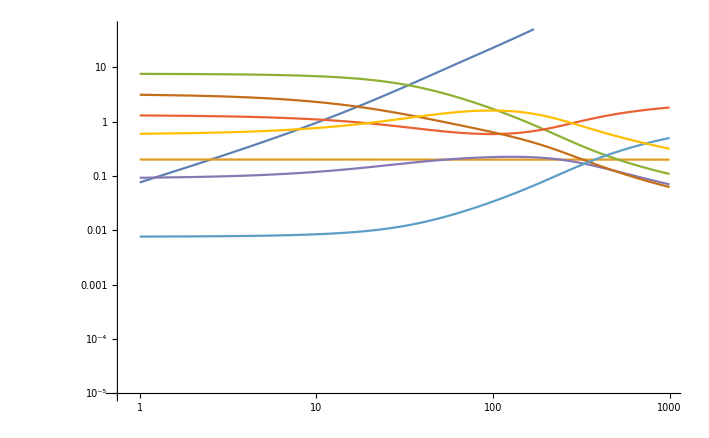

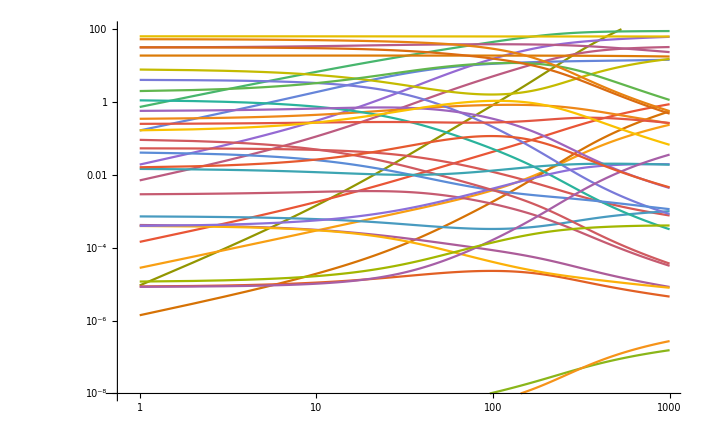

```mathematica
Show[
Table[
ListLogLogPlot[
Transpose[{mRange,solArray[[All,k]]}],Joined->True,PlotRange->{0.00001,50},PlotStyle->ColorData[97][k] 
],{k,1,n}]
]

Show[Table[
ListLogLogPlot[
Transpose[{mRange,soldijArray[[All,k]]}],Joined->True,PlotRange->{10^-8,100},PlotStyle->ColorData[97][k+n+1] 
],{k,1,Dimensions[soldijArray][[2]]}]
]
```

```mathematica
ClearAll["Global`*"];

signChangeCount[yValues_]:=Module[{signChanges,prevSign,dy},
dy = yValues[[2;;]]-yValues[[1;;-2]];
signChanges=0;
prevSign=Sign[First[dy]];
Do[If[Sign[dy[[i]]]!=prevSign,signChanges++;
prevSign=Sign[dy[[i]]];],{i,2,Length[dy]}];
signChanges]

mRange=Range[0,500,1];
n=3;
cVars=Array[c,n];


μ=1;
σ=5;

nIters = 1000;
seedArray = Range[nIters]+500;
SeedRandom[41];
SeedRandom[91];

scmFullList={};
solmFullList = {};
scdFullList={};
soldFullList = {};

kValsList = {};
mValsList = {};

Do[(*iter*)

mVals=RandomReal[{0.1,50.0},n];
kVals=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];
kVals=0.5 (kVals+Transpose[kVals]);(*make symmetric*)

AppendTo[kValsList,kVals];
AppendTo[mValsList,mVals];

scmSubList={};
solmSubList = {};
scdSubList={};
soldSubList = {};

Do[ (*mInd*)
initialGuess=Table[cVars[[i]]->RandomReal[{0.1,2.0}],{i,1,n}];
solmArray={};
soldArray={};

Do[(*mv*)
mValsNew=ReplacePart[mVals,mInd->mv];
eqnsSym=Table[Sum[cVars[[i]]*cVars[[j]]*kVals[[i,j]]^-1,{j,1,n}]+cVars[[i]]-mValsNew[[i]],{i,1,n}];
sol=Quiet@FindRoot[eqnsSym,Table[{cVars[[i]],cVars[[i]]/. initialGuess},{i,1,n}]];
cSol=cVars/. sol;
AppendTo[solmArray,cSol];
dij=kVals^-1*KroneckerProduct[cSol,cSol];
upperTriangleList=Flatten[Table[dij[[i,j]],{i,1,n},{j,i,n}]];

AppendTo[soldArray,upperTriangleList];
initialGuess=sol;
,{mv,mRange}];

(*Count sign changes in c[i] values over mRange*)
scmList=Table[signChangeCount[solmArray[[All,i]]]
,{i,1,n}];

(*Count sign changes in d_ij values*)
scdList=Table[signChangeCount[soldArray[[All,i]]],
{i,1,Dimensions[soldArray][[2]]}];

AppendTo[scmSubList,scmList];
AppendTo[scdSubList,scdList];

AppendTo[solmSubList, solmArray];
AppendTo[soldSubList, soldArray];
,{mInd,1,n}];

AppendTo[scmFullList,scmSubList];
AppendTo[scdFullList,scdSubList];
AppendTo[solmFullList, solmSubList];
AppendTo[soldFullList, soldSubList];

,{iter,1,nIters}];
```

```mathematica
val = 2;

Do[
Do[
Do[
If[scdFullList[[m,j,k]]==val,Print["d",m," ",j," ", k]];
,{k,1,Length[scdFullList[[1,1]]]}]
,{j,1,Length[scdFullList[[1]]]}]
,{m,1,Length[scdFullList]}]

Do[
Do[
Do[
If[scmFullList[[m,j,k]]==val,Print["m",m," ",j," ", k]];
,{k,1,Length[scmFullList[[1,1]]]}]
,{j,1,Length[scmFullList[[1]]]}]
,{m,1,Length[scmFullList]}]
```

d73 2 5

d209 1 2

d351 1 2

d351 2 2

d564 1 2

d564 2 2

d690 1 6

d768 1 2

d991 2 5

d991 3 5

m690 1 3

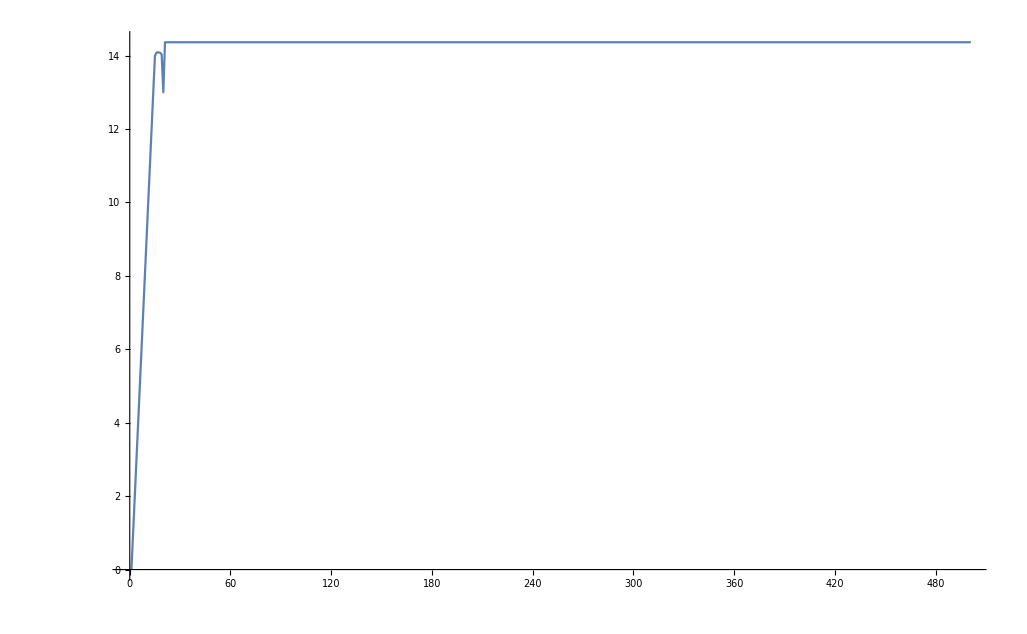

```mathematica
Show[
ListPlot[soldFullList[[768,1,;;,2]],Joined->True,PlotRange->{{0,500},Full}]]
```

```mathematica
(*scmFullList
scdFullList*)
```

```mathematica
n=3;

(*Variables*)
cVars=Array[c,n];


viewIter = 768;
viewMInd = 1;

mVals = mValsList[[viewIter]];
kVals = kValsList[[viewIter]];

(*Parameters for the log-normal distribution*)
μ=1;       (*Mean of the underlying normal distribution*)
σ=5;       (*Standard deviation*)



(*Assign random positive starting point for each variable*)
initialGuess=Table[cVars[[i]]->RandomReal[{0.1,2.0}],{i,1,n}];

mInd = viewMInd;
mRange = Range[0,500,0.1];
solArray = {};
soldijArray = {};
Do[
mVals[[mInd]]=mv;
eqnsSym=Table[Sum[cVars[[i]] *cVars[[j]] *kVals[[i,j]]^-1,{j,1,n}]+cVars[[i]]-mVals[[i]],{i,1,n}];
sol=FindRoot[eqnsSym, Table[{cVars[[i]],cVars[[i]]/.initialGuess},{i,1,n}],AccuracyGoal->10,PrecisionGoal->10, MaxIterations->1000];
cSol =  cVars/.sol;
AppendTo[solArray,cSol];

dij=kVals^-1*KroneckerProduct[cSol, cSol];

upperTriangleList=Flatten[Table[dij[[i,j]],{i,1,n},{j,i,n}]];
AppendTo[soldijArray,upperTriangleList];

initialGuess=sol;
,{mv,mRange}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

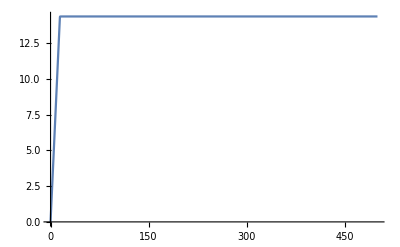

```mathematica
ListPlot[
Transpose[{mRange,soldijArray[[All,2]]}],Joined->True,PlotRange->Full,PlotStyle->ColorData[97][1] 
]
```

```mathematica
diagTerm = Table[Sum[kVals[[i,j]]^-1 cVars[[j]],{j,1,n}]+1,{i,1,n}];
offDiagTerm = Table[cVars[[i]] kVals[[i,j]]^-1,{i,1,n},{j,1,n}];
JMat = DiagonalMatrix[diagTerm]+offDiagTerm;
JInv = Inverse[JMat];
```

```mathematica
solArray[[1]]
```

{27.1762,1.05507×10^-20,0.138659,22.6948}

```mathematica
matEl//Numerator
```

0.-0.00227845 c[4]+0.263787 c[1] c[4]+0.89509 c[1]^2 c[4]-0.135118 c[2] c[4]-0.327979 c[1] c[2] c[4]-0.0566811 c[2]^2 c[4]-0.000883532 c[3] c[4]-3.06393 c[1] c[3] c[4]+0.387408 c[2] c[3] c[4]+0.0218855 c[3]^2 c[4]-0.0000463915 c[4]^2+0.00423926 c[1] c[4]^2-0.0021178 c[2] c[4]^2-0.0000878514 c[3] c[4]^2-1.65388×10^-7 c[4]^3

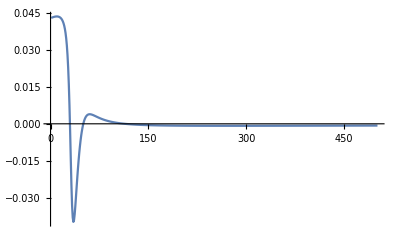

```mathematica
matEl=JInv[[4,viewMInd]];
evalFunc[sol_]:=Table[cVars[[k]]->sol[[k]],{k,1,n}];
ListPlot[Table[matEl/.evalFunc[solArray[[k]]],{k,1,Length[mRange]}],Joined->True,PlotRange->Full]
```

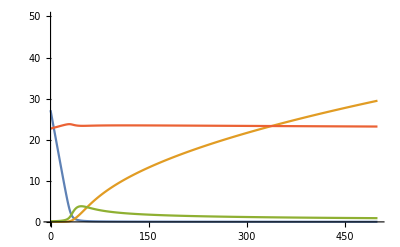

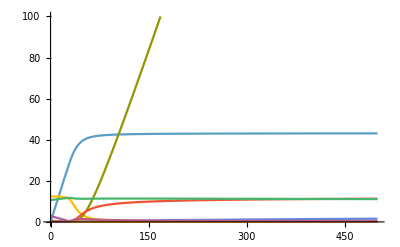

```mathematica
Show[
Table[
ListPlot[
Transpose[{mRange,solArray[[All,k]]}],Joined->True,PlotRange->{0.00001,50},PlotStyle->ColorData[97][k] 
],{k,1,n}]
]

Show[Table[
ListPlot[
Transpose[{mRange,soldijArray[[All,k]]}],Joined->True,PlotRange->{10^-8,100},PlotStyle->ColorData[97][k+n+1] 
],{k,1,Dimensions[soldijArray][[2]]}]
]
```

#### Analytical sols

```mathematica
nd = 4;
Qf = Table[CC[i]*KK[i,j],{i,1,nd},{j,1,nd}];
Qd = DiagonalMatrix[Table[1+Sum[KK[i,j]CC[j],{j,1,nd}],{i,1,nd}]];
Qmat = Qf+Qd;
```

```mathematica
Qmat//MatrixForm
Drop[Qmat,{1},{2}]//MatrixForm
```

(1+2 CC[1] KK[1,1]+CC[2] KK[1,2]+CC[3] KK[1,3]+CC[4] KK[1,4] | CC[1] KK[1,2] | CC[1] KK[1,3] | CC[1] KK[1,4]
CC[2] KK[2,1] | 1+CC[1] KK[2,1]+2 CC[2] KK[2,2]+CC[3] KK[2,3]+CC[4] KK[2,4] | CC[2] KK[2,3] | CC[2] KK[2,4]
CC[3] KK[3,1] | CC[3] KK[3,2] | 1+CC[1] KK[3,1]+CC[2] KK[3,2]+2 CC[3] KK[3,3]+CC[4] KK[3,4] | CC[3] KK[3,4]
CC[4] KK[4,1] | CC[4] KK[4,2] | CC[4] KK[4,3] | 1+CC[1] KK[4,1]+CC[2] KK[4,2]+CC[3] KK[4,3]+2 CC[4] KK[4,4])

(CC[2] KK[2,1] | CC[2] KK[2,3] | CC[2] KK[2,4]
CC[3] KK[3,1] | 1+CC[1] KK[3,1]+CC[2] KK[3,2]+2 CC[3] KK[3,3]+CC[4] KK[3,4] | CC[3] KK[3,4]
CC[4] KK[4,1] | CC[4] KK[4,3] | 1+CC[1] KK[4,1]+CC[2] KK[4,2]+CC[3] KK[4,3]+2 CC[4] KK[4,4])

```mathematica
-Det[Drop[Qmat,{1},{2}]]-Adjugate[Qmat][[2,1]]//Simplify
```

0

```mathematica
expr=Adjugate[Qmat][[2,1]]//MonomialList
```

{CC[2] CC[3]^2 KK[2,3] KK[3,1] KK[4,3],-2 CC[2] CC[3]^2 KK[2,1] KK[3,3] KK[4,3],-CC[2] CC[3] CC[4] KK[2,3] KK[3,4] KK[4,1],CC[2]^2 CC[3] KK[2,3] KK[3,1] KK[4,2],-CC[2]^2 CC[3] KK[2,1] KK[3,2] KK[4,3],-2 CC[2]^2 CC[3] KK[2,1] KK[3,3] KK[4,2],2 CC[2] CC[3] CC[4] KK[2,3] KK[3,1] KK[4,4],2 CC[2] CC[3] CC[4] KK[2,4] KK[3,3] KK[4,1],-4 CC[2] CC[3] CC[4] KK[2,1] KK[3,3] KK[4,4],-CC[2] CC[3] CC[4] KK[2,4] KK[3,1] KK[4,3],CC[1] CC[2] CC[3] KK[2,3] KK[3,1] KK[4,1],CC[2] CC[3] KK[2,3] KK[3,1],-2 CC[1] CC[2] CC[3] KK[2,1] KK[3,3] KK[4,1],-CC[1] CC[2] CC[3] KK[2,1] KK[3,1] KK[4,3],-CC[2] CC[3] KK[2,1] KK[4,3],-2 CC[2] CC[3] KK[2,1] KK[3,3],-CC[2]^2 CC[4] KK[2,1] KK[3,4] KK[4,2],CC[2] CC[4]^2 KK[2,4] KK[3,4] KK[4,1],-2 CC[2] CC[4]^2 KK[2,1] KK[3,4] KK[4,4],-CC[1] CC[2] CC[4] KK[2,1] KK[3,4] KK[4,1],-CC[2] CC[4] KK[2,1] KK[3,4],-CC[2]^3 KK[2,1] KK[3,2] KK[4,2],CC[2]^2 CC[4] KK[2,4] KK[3,2] KK[4,1],-2 CC[2]^2 CC[4] KK[2,1] KK[3,2] KK[4,4],-CC[1] CC[2]^2 KK[2,1] KK[3,2] KK[4,1],-CC[1] CC[2]^2 KK[2,1] KK[3,1] KK[4,2],-CC[2]^2 KK[2,1] KK[3,2],-CC[2]^2 KK[2,1] KK[4,2],CC[1] CC[2] CC[4] KK[2,4] KK[3,1] KK[4,1],CC[2] CC[4] KK[2,4] KK[4,1],-2 CC[1] CC[2] CC[4] KK[2,1] KK[3,1] KK[4,4],-2 CC[2] CC[4] KK[2,1] KK[4,4],-CC[1]^2 CC[2] KK[2,1] KK[3,1] KK[4,1],-CC[1] CC[2] KK[2,1] KK[4,1],-CC[1] CC[2] KK[2,1] KK[3,1],-CC[2] KK[2,1]}

```mathematica
expr=Adjugate[Qmat][[2,1]]
MonomialList[expr]//TraditionalForm

expr=Adjugate[Qmat][[1,2]];
MonomialList[expr]//TraditionalForm
(*D[MonomialList[expr],CC[2]]//TraditionalForm
MonomialList[expr]/D[MonomialList[expr],CC[2]]*)
```

CC[3] KK[3,4] (-CC[2] CC[4] KK[2,3] KK[4,1]+CC[2] CC[4] KK[2,1] KK[4,3])+CC[2] KK[2,4] (CC[4] KK[4,1]+CC[1] CC[4] KK[3,1] KK[4,1]+CC[2] CC[4] KK[3,2] KK[4,1]+2 CC[3] CC[4] KK[3,3] KK[4,1]+CC[4]^2 KK[3,4] KK[4,1]-CC[3] CC[4] KK[3,1] KK[4,3])+(-CC[2] KK[2,1]-CC[1] CC[2] KK[2,1] KK[3,1]+CC[2] CC[3] KK[2,3] KK[3,1]-CC[2]^2 KK[2,1] KK[3,2]-2 CC[2] CC[3] KK[2,1] KK[3,3]-CC[2] CC[4] KK[2,1] KK[3,4]) (1+CC[1] KK[4,1]+CC[2] KK[4,2]+CC[3] KK[4,3]+2 CC[4] KK[4,4])

{CC(2) (CC(3))^2 KK(2,3) KK(3,1) KK(4,3),-2 CC(2) (CC(3))^2 KK(2,1) KK(3,3) KK(4,3),-CC(2) CC(3) CC(4) KK(2,3) KK(3,4) KK(4,1),(CC(2))^2 CC(3) KK(2,3) KK(3,1) KK(4,2),-(CC(2))^2 CC(3) KK(2,1) KK(3,2) KK(4,3),-2 (CC(2))^2 CC(3) KK(2,1) KK(3,3) KK(4,2),2 CC(2) CC(3) CC(4) KK(2,3) KK(3,1) KK(4,4),2 CC(2) CC(3) CC(4) KK(2,4) KK(3,3) KK(4,1),-4 CC(2) CC(3) CC(4) KK(2,1) KK(3,3) KK(4,4),-CC(2) CC(3) CC(4) KK(2,4) KK(3,1) KK(4,3),CC(1) CC(2) CC(3) KK(2,3) KK(3,1) KK(4,1),CC(2) CC(3) KK(2,3) KK(3,1),-2 CC(1) CC(2) CC(3) KK(2,1) KK(3,3) KK(4,1),-CC(1) CC(2) CC(3) KK(2,1) KK(3,1) KK(4,3),-CC(2) CC(3) KK(2,1) KK(4,3),-2 CC(2) CC(3) KK(2,1) KK(3,3),-(CC(2))^2 CC(4) KK(2,1) KK(3,4) KK(4,2),CC(2) (CC(4))^2 KK(2,4) KK(3,4) KK(4,1),-2 CC(2) (CC(4))^2 KK(2,1) KK(3,4) KK(4,4),-CC(1) CC(2) CC(4) KK(2,1) KK(3,4) KK(4,1),-CC(2) CC(4) KK(2,1) KK(3,4),-(CC(2))^3 KK(2,1) KK(3,2) KK(4,2),(CC(2))^2 CC(4) KK(2,4) KK(3,2) KK(4,1),-2 (CC(2))^2 CC(4) KK(2,1) KK(3,2) KK(4,4),-CC(1) (CC(2))^2 KK(2,1) KK(3,2) KK(4,1),-CC(1) (CC(2))^2 KK(2,1) KK(3,1) KK(4,2),-(CC(2))^2 KK(2,1) KK(3,2),-(CC(2))^2 KK(2,1) KK(4,2),CC(1) CC(2) CC(4) KK(2,4) KK(3,1) KK(4,1),CC(2) CC(4) KK(2,4) KK(4,1),-2 CC(1) CC(2) CC(4) KK(2,1) KK(3,1) KK(4,4),-2 CC(2) CC(4) KK(2,1) KK(4,4),-(CC(1))^2 CC(2) KK(2,1) KK(3,1) KK(4,1),-CC(1) CC(2) KK(2,1) KK(4,1),-CC(1) CC(2) KK(2,1) KK(3,1),-CC(2) KK(2,1)}

{CC(1) (CC(3))^2 KK(1,3) KK(3,2) KK(4,3),-2 CC(1) (CC(3))^2 KK(1,2) KK(3,3) KK(4,3),-CC(1) CC(3) CC(4) KK(1,3) KK(3,4) KK(4,2),(CC(1))^2 CC(3) KK(1,3) KK(3,2) KK(4,1),-(CC(1))^2 CC(3) KK(1,2) KK(3,1) KK(4,3),-2 (CC(1))^2 CC(3) KK(1,2) KK(3,3) KK(4,1),2 CC(1) CC(3) CC(4) KK(1,3) KK(3,2) KK(4,4),2 CC(1) CC(3) CC(4) KK(1,4) KK(3,3) KK(4,2),-4 CC(1) CC(3) CC(4) KK(1,2) KK(3,3) KK(4,4),-CC(1) CC(3) CC(4) KK(1,4) KK(3,2) KK(4,3),CC(1) CC(2) CC(3) KK(1,3) KK(3,2) KK(4,2),CC(1) CC(3) KK(1,3) KK(3,2),-2 CC(1) CC(2) CC(3) KK(1,2) KK(3,3) KK(4,2),-CC(1) CC(2) CC(3) KK(1,2) KK(3,2) KK(4,3),-CC(1) CC(3) KK(1,2) KK(4,3),-2 CC(1) CC(3) KK(1,2) KK(3,3),-(CC(1))^2 CC(4) KK(1,2) KK(3,4) KK(4,1),CC(1) (CC(4))^2 KK(1,4) KK(3,4) KK(4,2),-2 CC(1) (CC(4))^2 KK(1,2) KK(3,4) KK(4,4),-CC(1) CC(2) CC(4) KK(1,2) KK(3,4) KK(4,2),-CC(1) CC(4) KK(1,2) KK(3,4),-(CC(1))^3 KK(1,2) KK(3,1) KK(4,1),(CC(1))^2 CC(4) KK(1,4) KK(3,1) KK(4,2),-2 (CC(1))^2 CC(4) KK(1,2) KK(3,1) KK(4,4),-(CC(1))^2 CC(2) KK(1,2) KK(3,1) KK(4,2),-(CC(1))^2 KK(1,2) KK(3,1),-(CC(1))^2 CC(2) KK(1,2) KK(3,2) KK(4,1),-(CC(1))^2 KK(1,2) KK(4,1),CC(1) CC(2) CC(4) KK(1,4) KK(3,2) KK(4,2),CC(1) CC(4) KK(1,4) KK(4,2),-2 CC(1) CC(2) CC(4) KK(1,2) KK(3,2) KK(4,4),-2 CC(1) CC(4) KK(1,2) KK(4,4),-CC(1) (CC(2))^2 KK(1,2) KK(3,2) KK(4,2),-CC(1) CC(2) KK(1,2) KK(4,2),-CC(1) CC(2) KK(1,2) KK(3,2),-CC(1) KK(1,2)}

```mathematica
expr//Expand
```

1+2 CC[1] KK[1,1]+CC[2] KK[1,2]+CC[3] KK[1,3]+CC[4] KK[1,4]+CC[1] KK[3,1]+2 CC[1]^2 KK[1,1] KK[3,1]+CC[1] CC[2] KK[1,2] KK[3,1]+CC[1] CC[4] KK[1,4] KK[3,1]+CC[2] KK[3,2]+2 CC[1] CC[2] KK[1,1] KK[3,2]+CC[2]^2 KK[1,2] KK[3,2]+CC[2] CC[3] KK[1,3] KK[3,2]+CC[2] CC[4] KK[1,4] KK[3,2]+2 CC[3] KK[3,3]+4 CC[1] CC[3] KK[1,1] KK[3,3]+2 CC[2] CC[3] KK[1,2] KK[3,3]+2 CC[3]^2 KK[1,3] KK[3,3]+2 CC[3] CC[4] KK[1,4] KK[3,3]+CC[4] KK[3,4]+2 CC[1] CC[4] KK[1,1] KK[3,4]+CC[2] CC[4] KK[1,2] KK[3,4]+CC[3] CC[4] KK[1,3] KK[3,4]+CC[4]^2 KK[1,4] KK[3,4]+CC[1] KK[4,1]+2 CC[1]^2 KK[1,1] KK[4,1]+CC[1] CC[2] KK[1,2] KK[4,1]+CC[1] CC[3] KK[1,3] KK[4,1]+CC[1]^2 KK[3,1] KK[4,1]+2 CC[1]^3 KK[1,1] KK[3,1] KK[4,1]+CC[1]^2 CC[2] KK[1,2] KK[3,1] KK[4,1]+CC[1] CC[2] KK[3,2] KK[4,1]+2 CC[1]^2 CC[2] KK[1,1] KK[3,2] KK[4,1]+CC[1] CC[2]^2 KK[1,2] KK[3,2] KK[4,1]+CC[1] CC[2] CC[3] KK[1,3] KK[3,2] KK[4,1]+2 CC[1] CC[3] KK[3,3] KK[4,1]+4 CC[1]^2 CC[3] KK[1,1] KK[3,3] KK[4,1]+2 CC[1] CC[2] CC[3] KK[1,2] KK[3,3] KK[4,1]+2 CC[1] CC[3]^2 KK[1,3] KK[3,3] KK[4,1]+CC[1] CC[4] KK[3,4] KK[4,1]+2 CC[1]^2 CC[4] KK[1,1] KK[3,4] KK[4,1]+CC[1] CC[2] CC[4] KK[1,2] KK[3,4] KK[4,1]+2 CC[1] CC[3] CC[4] KK[1,3] KK[3,4] KK[4,1]+CC[2] KK[4,2]+2 CC[1] CC[2] KK[1,1] KK[4,2]+CC[2]^2 KK[1,2] KK[4,2]+CC[2] CC[3] KK[1,3] KK[4,2]+CC[2] CC[4] KK[1,4] KK[4,2]+CC[1] CC[2] KK[3,1] KK[4,2]+2 CC[1]^2 CC[2] KK[1,1] KK[3,1] KK[4,2]+CC[1] CC[2]^2 KK[1,2] KK[3,1] KK[4,2]+CC[1] CC[2] CC[4] KK[1,4] KK[3,1] KK[4,2]+CC[2]^2 KK[3,2] KK[4,2]+2 CC[1] CC[2]^2 KK[1,1] KK[3,2] KK[4,2]+CC[2]^3 KK[1,2] KK[3,2] KK[4,2]+CC[2]^2 CC[3] KK[1,3] KK[3,2] KK[4,2]+CC[2]^2 CC[4] KK[1,4] KK[3,2] KK[4,2]+2 CC[2] CC[3] KK[3,3] KK[4,2]+4 CC[1] CC[2] CC[3] KK[1,1] KK[3,3] KK[4,2]+2 CC[2]^2 CC[3] KK[1,2] KK[3,3] KK[4,2]+2 CC[2] CC[3]^2 KK[1,3] KK[3,3] KK[4,2]+2 CC[2] CC[3] CC[4] KK[1,4] KK[3,3] KK[4,2]+CC[2] CC[4] KK[3,4] KK[4,2]+2 CC[1] CC[2] CC[4] KK[1,1] KK[3,4] KK[4,2]+CC[2]^2 CC[4] KK[1,2] KK[3,4] KK[4,2]+CC[2] CC[3] CC[4] KK[1,3] KK[3,4] KK[4,2]+CC[2] CC[4]^2 KK[1,4] KK[3,4] KK[4,2]+CC[3] KK[4,3]+2 CC[1] CC[3] KK[1,1] KK[4,3]+CC[2] CC[3] KK[1,2] KK[4,3]+CC[3]^2 KK[1,3] KK[4,3]+CC[3] CC[4] KK[1,4] KK[4,3]+CC[1] CC[3] KK[3,1] KK[4,3]+2 CC[1]^2 CC[3] KK[1,1] KK[3,1] KK[4,3]+CC[1] CC[2] CC[3] KK[1,2] KK[3,1] KK[4,3]+2 CC[1] CC[3] CC[4] KK[1,4] KK[3,1] KK[4,3]+CC[2] CC[3] KK[3,2] KK[4,3]+2 CC[1] CC[2] CC[3] KK[1,1] KK[3,2] KK[4,3]+CC[2]^2 CC[3] KK[1,2] KK[3,2] KK[4,3]+CC[2] CC[3]^2 KK[1,3] KK[3,2] KK[4,3]+CC[2] CC[3] CC[4] KK[1,4] KK[3,2] KK[4,3]+2 CC[3]^2 KK[3,3] KK[4,3]+4 CC[1] CC[3]^2 KK[1,1] KK[3,3] KK[4,3]+2 CC[2] CC[3]^2 KK[1,2] KK[3,3] KK[4,3]+2 CC[3]^3 KK[1,3] KK[3,3] KK[4,3]+2 CC[3]^2 CC[4] KK[1,4] KK[3,3] KK[4,3]+2 CC[4] KK[4,4]+4 CC[1] CC[4] KK[1,1] KK[4,4]+2 CC[2] CC[4] KK[1,2] KK[4,4]+2 CC[3] CC[4] KK[1,3] KK[4,4]+2 CC[4]^2 KK[1,4] KK[4,4]+2 CC[1] CC[4] KK[3,1] KK[4,4]+4 CC[1]^2 CC[4] KK[1,1] KK[3,1] KK[4,4]+2 CC[1] CC[2] CC[4] KK[1,2] KK[3,1] KK[4,4]+2 CC[1] CC[4]^2 KK[1,4] KK[3,1] KK[4,4]+2 CC[2] CC[4] KK[3,2] KK[4,4]+4 CC[1] CC[2] CC[4] KK[1,1] KK[3,2] KK[4,4]+2 CC[2]^2 CC[4] KK[1,2] KK[3,2] KK[4,4]+2 CC[2] CC[3] CC[4] KK[1,3] KK[3,2] KK[4,4]+2 CC[2] CC[4]^2 KK[1,4] KK[3,2] KK[4,4]+4 CC[3] CC[4] KK[3,3] KK[4,4]+8 CC[1] CC[3] CC[4] KK[1,1] KK[3,3] KK[4,4]+4 CC[2] CC[3] CC[4] KK[1,2] KK[3,3] KK[4,4]+4 CC[3]^2 CC[4] KK[1,3] KK[3,3] KK[4,4]+4 CC[3] CC[4]^2 KK[1,4] KK[3,3] KK[4,4]+2 CC[4]^2 KK[3,4] KK[4,4]+4 CC[1] CC[4]^2 KK[1,1] KK[3,4] KK[4,4]+2 CC[2] CC[4]^2 KK[1,2] KK[3,4] KK[4,4]+2 CC[3] CC[4]^2 KK[1,3] KK[3,4] KK[4,4]+2 CC[4]^3 KK[1,4] KK[3,4] KK[4,4]

```mathematica
D[expr,CC[2]]//Simplify
```

CC[3] KK[2,3] KK[3,1]-KK[2,1] (1+CC[1] KK[3,1]+2 CC[2] KK[3,2]+2 CC[3] KK[3,3])

```mathematica
eqs
```

{CC[1]-Ct[1]+CC[1] KK[1,j]+CC[2] KK[1,j]+CC[3] KK[1,j]+CC[4] KK[1,j]==0,CC[2]-Ct[2]+CC[1] KK[2,j]+CC[2] KK[2,j]+CC[3] KK[2,j]+CC[4] KK[2,j]==0,CC[3]-Ct[3]+CC[1] KK[3,j]+CC[2] KK[3,j]+CC[3] KK[3,j]+CC[4] KK[3,j]==0,CC[4]-Ct[4]+CC[1] KK[4,j]+CC[2] KK[4,j]+CC[3] KK[4,j]+CC[4] KK[4,j]==0}

```mathematica
n = 2;
eqs = Table[CC[i]+Sum[KK[i,j]CC[i]CC[j],{j,1,n}]-Ct[i]==0,{i,1,n}];
cVars =Table[CC[i],{i,1,n}];
sol=Solve[eqs,cVars]
```

```mathematica
eqs = {kAB BB == kBA AA, kDA AA == kAD DD,kBD DD == kDB BB, kCD DD==kDC CC, kED DD ==k DE EE, kCB BB == kBC CC, kEC CC==kCE EE };
Solve[eqs,{AA,BB,CC,DD,EE}]
```

{{AA→0,BB→0,CC→0,DD→0,EE→0}}

#### Derivative space

(6.12374 | 0.00754095 | 0.312261
0.00754095 | 1649.54 | 73.8645
0.312261 | 73.8645 | 0.710569)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

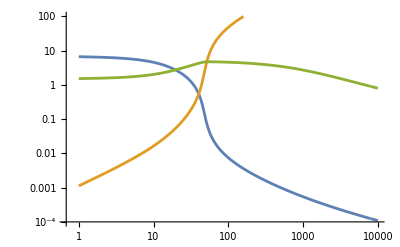

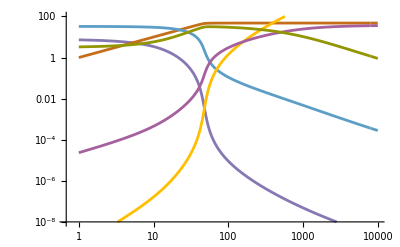

```mathematica
ClearAll["Global`*"];

n=3;

(*Variables*)
cVars=Array[c,n];

seed = RandomInteger[1000];
(*seed = 794;*)
(*seed = 155*)
SeedRandom[seed];  


(*reproducibility*)
mVals=RandomReal[{0.1,100.0},n];

kVals=RandomReal[{0.01,10.0},{n,n}];

(*Parameters for the log-normal distribution*)
μ=1;       (*Mean of the underlying normal distribution*)
σ=5;       (*Standard deviation*)

(*Sample kVals as log-normally distributed*)
kVals=RandomVariate[LogNormalDistribution[μ,σ],{n,n}];
Do[If[i>j,kVals[[i,j]]=kVals[[j,i]]],{i,n},{j,n}];
kVals//MatrixForm

(*Assign random positive starting point for each variable*)
initialGuess=Table[cVars[[i]]->RandomReal[{0.1,2.0}],{i,1,n}];

mInd = 2;
mRange = Range[0,10000,1];
solArray = {};
soldijArray = {};
Do[
mVals[[mInd]]=mv;
eqnsSym=Table[Sum[cVars[[i]] *cVars[[j]] *kVals[[i,j]]^-1,{j,1,n}]+cVars[[i]]-mVals[[i]],{i,1,n}];
sol=FindRoot[eqnsSym, Table[{cVars[[i]],cVars[[i]]/.initialGuess},{i,1,n}], AccuracyGoal->5, PrecisionGoal->10];
cSol =  cVars/.sol;
AppendTo[solArray,cSol];

dij=kVals^-1*KroneckerProduct[cSol, cSol];

upperTriangleList=Flatten[Table[dij[[i,j]],{i,1,n},{j,i,n}]];
AppendTo[soldijArray,upperTriangleList];

initialGuess=sol;
,{mv,mRange}];

Show[
Table[
ListLogLogPlot[
Transpose[{mRange,solArray[[All,k]]}],Joined->True,PlotRange->{0.0001,100},PlotStyle->ColorData[97][k] 
],{k,1,n}]
]

Show[Table[
ListLogLogPlot[
Transpose[{mRange,soldijArray[[All,k]]}],Joined->True,PlotRange->{10^-8,100},PlotStyle->ColorData[97][k+n+1] 
],{k,1,Dimensions[soldijArray][[2]]}]
]

(*Show[
Table[
ListPlot[
Transpose[{mRange,solArray[[All,k]]}],Joined->True,PlotRange->{0.001,100},PlotStyle->ColorData[97][k] 
],{k,1,n}]
]

Show[Table[
ListPlot[
Transpose[{mRange,soldijArray[[All,k]]}],Joined->True,PlotRange->{10^-8,100},PlotStyle->ColorData[97][k+n+1] 
],{k,1,Dimensions[soldijArray][[2]]}]
]*)
```

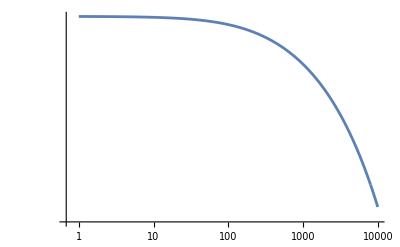

```mathematica
ListLogLogPlot[
Transpose[{mRange,solArray[[All,1]]}],Joined->True,PlotStyle->ColorData[97][k] 
]
```

```mathematica
Qf = Table[cVars[[i]]*kVals[[i,j]]^-1,{i,1,n},{j,1,n}];
Qd = DiagonalMatrix[Table[1+Sum[kVals[[i,j]]^-1*cVars[[j]],{j,1,n}],{i,1,n}]];
Qmat = Qf+Qd;
expr=Adjugate[Qmat][[3,mInd]]
MonomialList[expr]//TraditionalForm
```

0.-0.0135383 c[3]+424.67 c[1] c[3]-1.7953 c[2] c[3]-0.0433557 c[3]^2

{-0.0433557 (c(3))^2,424.67 c(1) c(3),-1.7953 c(2) c(3),-0.0135383 c(3)}

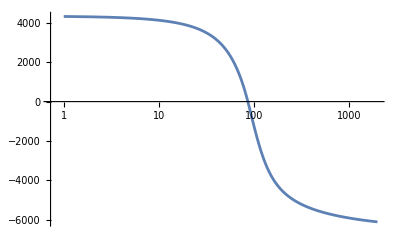

```mathematica
JInv = Inverse[Qmat];
matEl=JInv[[3,mInd]];
evalFunc[sol_]:=Table[cVars[[k]]->sol[[k]],{k,1,n}];
ListLogLinearPlot[Table[expr/.evalFunc[solArray[[k]]],{k,1,Length[mRange]}],Joined->True,PlotRange->Full]
```

```mathematica
exprs=Adjugate[Qmat][[;;,mInd]];

cMin = 0.0001;
cMax = 1;
Show[
ContourPlot3D[exprs,{c[1],cMin,cMax},{c[2],cMin,cMax},{c[3],cMin,cMax},AxesLabel->{"c1","c2","c3"},PlotPoints->50],
ListLinePlot3D[solArray]
]
```

-Graphics3D-

```mathematica
exprs[[1]]
```

0.-134.834 c[1]-6.03633 c[1]^2-8.12385 c[1] c[2]-0.00134781 c[1] c[3]

```mathematica
nd = 3;
QfSym = Table[cVars[[i]]*KK[i,j],{i,1,nd},{j,1,nd}];
QdSym = DiagonalMatrix[Table[1+Sum[KK[i,j]cVars[[j]],{j,1,nd}],{i,1,nd}]];
QmatSym = QfSym+QdSym;
```

Part::partd: Part specification cVars⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification cVars⟦1⟧ is longer than depth of object.

Part::partd: Part specification cVars⟦2⟧ is longer than depth of object.

Part::partd: Part specification cVars⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
expr=Adjugate[Qmat][[3,mInd]]
exprSym =Adjugate[QmatSym][[3,mInd]]
```

0.-0.0602509 c[3]+6.03569 c[1] c[3]-8.12385 c[2] c[3]-0.00269736 c[3]^2

c[1] c[3] KK[1,2] KK[3,1]-c[3] KK[3,2]-2 c[1] c[3] KK[1,1] KK[3,2]-c[2] c[3] KK[1,2] KK[3,2]-c[3]^2 KK[1,3] KK[3,2]

```mathematica
MonomialList[expr]
MonomialList[exprSym]
```

{-0.00269736 c[3]^2,6.03569 c[1] c[3],-8.12385 c[2] c[3],-0.0602509 c[3]}

{c[1] c[3] KK[1,2] KK[3,1],-2 c[1] c[3] KK[1,1] KK[3,2],-c[3]^2 KK[1,3] KK[3,2],-c[2] c[3] KK[1,2] KK[3,2],-c[3] KK[3,2]}

```mathematica
Table[((2(nl-2))^nl nl^nl)/Factorial[nl],{nl,2,5}]//N
```

{0.,36.,2730.67,202500.}

```mathematica
Table[(2^nl nl^nl)/Factorial[nl],{nl,2,5}]//N
```

{8.,36.,170.667,833.333}

```mathematica
nd = 3;
symmetryRules=Flatten[Table[If[i>j,KK[i,j]->KK[j,i],Nothing],{i,1,nd},{j,1,nd}]];
QfSym = Table[CC[i]*KK[i,j],{i,1,nd},{j,1,nd}];
QdSym = DiagonalMatrix[Table[1+Sum[KK[i,j]CC[j],{j,1,nd}],{i,1,nd}]];
QmatSym = QfSym+QdSym/.symmetryRules;

exprSym=Adjugate[QmatSym][[;;,1]]
```

{-CC[2] CC[3] KK[2,3]^2+(1+CC[1] KK[1,2]+2 CC[2] KK[2,2]+CC[3] KK[2,3]) (1+CC[1] KK[1,3]+CC[2] KK[2,3]+2 CC[3] KK[3,3]),-CC[2] KK[1,2]-CC[1] CC[2] KK[1,2] KK[1,3]-CC[2]^2 KK[1,2] KK[2,3]+CC[2] CC[3] KK[1,3] KK[2,3]-2 CC[2] CC[3] KK[1,2] KK[3,3],-CC[3] KK[1,3]-CC[1] CC[3] KK[1,2] KK[1,3]-2 CC[2] CC[3] KK[1,3] KK[2,2]+CC[2] CC[3] KK[1,2] KK[2,3]-CC[3]^2 KK[1,3] KK[2,3]}

```mathematica
swapCC[i_,j_][expr_]:=Module[{tmp},expr/. CC[i]->tmp/. CC[j]->CC[i]/. tmp->CC[j]]

swapCC[2,3][exprSym[[2]]]
exprSym[[3]]
```

CC[3] (KK[1,3] (1+CC[3] KK[2,3]+CC[2] (2 KK[2,2]+KK[2,3]))-KK[1,2] (1+CC[3] KK[2,3]+CC[2] (KK[2,3]+2 KK[3,3])))

```mathematica
exprSym[[2]]
swapCC[2,3][exprSym[[2]]]
exprSym[[3]]
```

-CC[2] KK[1,2]-CC[1] CC[2] KK[1,2] KK[1,3]-CC[2]^2 KK[1,2] KK[2,3]+CC[2] CC[3] KK[1,3] KK[2,3]-2 CC[2] CC[3] KK[1,2] KK[3,3]

-CC[3] KK[1,2]-CC[1] CC[3] KK[1,2] KK[1,3]-CC[3]^2 KK[1,2] KK[2,3]+CC[2] CC[3] KK[1,3] KK[2,3]-2 CC[2] CC[3] KK[1,2] KK[3,3]

-CC[3] KK[1,3]-CC[1] CC[3] KK[1,2] KK[1,3]-2 CC[2] CC[3] KK[1,3] KK[2,2]+CC[2] CC[3] KK[1,2] KK[2,3]-CC[3]^2 KK[1,3] KK[2,3]

```mathematica
Table[CC[i],{i,1,nd}]
```

{CC[1],CC[2],CC[3]}

```mathematica
MonomialList[exprSym[[2]],Table[CC[i],{i,1,nd}]] (* exchange 2,3 - symmetric interchange*)
MonomialList[exprSym[[3]],Table[CC[i],{i,1,nd}]]
```

{-CC[1] CC[2] KK[1,2] KK[1,3],-CC[2]^2 KK[1,2] KK[2,3],CC[2] CC[3] (KK[1,3] KK[2,3]-2 KK[1,2] KK[3,3]),-CC[2] KK[1,2]}

{-CC[1] CC[3] KK[1,2] KK[1,3],CC[2] CC[3] (-2 KK[1,3] KK[2,2]+KK[1,2] KK[2,3]),-CC[3]^2 KK[1,3] KK[2,3],-CC[3] KK[1,3]}

```mathematica
MonomialList[exprSym[[2]]/CC[2],Table[CC[i],{i,1,nd}]] (* exchange 2,3 *)
MonomialList[exprSym[[3]]/CC[3],Table[CC[i],{i,1,nd}]]
```

{-CC[1] KK[2,1] KK[3,1],-CC[2] KK[2,1] KK[3,2],CC[3] (KK[2,3] KK[3,1]-2 KK[2,1] KK[3,3]),-KK[2,1]}

{-CC[1] KK[2,1] KK[3,1],CC[2] (-2 KK[2,2] KK[3,1]+KK[2,1] KK[3,2]),-CC[3] KK[2,3] KK[3,1],-KK[3,1]}

```mathematica
Reduce[exprSym[[3]]>0,{CC[1],CC[2],CC[3]} ]
```